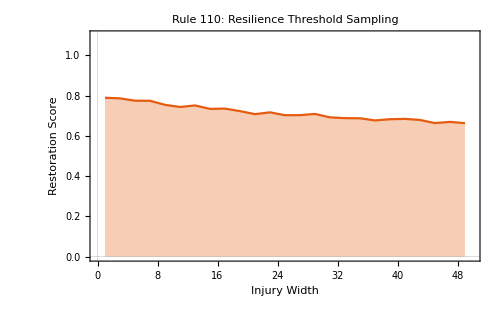

```mathematica
(*Resilience Sampling Function*)CalculateResilience[rule_,width_]:=Module[{steps=150,mixAt=50,init,clean,injured,diff,score},init=CenterArray[{1},301];
clean=CellularAutomaton[rule,init,steps];
(*Apply disruption at mixAt*)injured=Module[{pre,mid,post},pre=Take[clean,mixAt];
mid=Last[pre];
(*Random disruption of specified width*)mid[[151-width;;151+width]]=RandomInteger[1,2*width+1];
post=CellularAutomaton[rule,mid,steps-mixAt];
Join[pre,post]];
(*Difference Map XOR*)diff=MapThread[BitXor,{clean,injured},2];
(*Score:1.0=Perfect Healing;0.0=Total Failure*)score=1.0-(Total[Last[diff]]/Length[Last[diff]]);
score];

(*Sample Rule 110 across varying injury widths*)
samplingData=Table[{w,Mean[Table[CalculateResilience[110,w],{10}]]},{w,1,50,2}];

ListLinePlot[samplingData,PlotTheme->"Scientific",Frame->True,FrameLabel->{"Injury Width","Restoration Score"},PlotLabel->Style["Rule 110: Resilience Threshold Sampling",14,Bold],PlotRange->{{0,50},{0,1.1}},Filling->Bottom,ImageSize->500,ImagePadding->{{60,20},{50,20}} (*Adds space for the text*)]
```

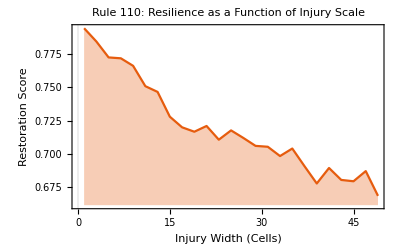

```mathematica
(*Function to calculate the percentage of recovery*)MeasureRecovery[rule_,injuryWidth_]:=Module[{steps=150,mixAt=50,init,clean,injured,diff},init=CenterArray[{1},301];
clean=CellularAutomaton[rule,init,steps];
(*Generate injured state*)injured=Module[{pre,mid,post},pre=Take[clean,mixAt];
mid=Last[pre];
(*Randomly perturb a section of width'injuryWidth'*)mid[[151-injuryWidth;;151+injuryWidth]]=RandomInteger[1,2*injuryWidth+1];
post=CellularAutomaton[rule,mid,steps-mixAt];
Join[pre,post]];
(*Calculate XOR Difference*)diff=MapThread[BitXor,{clean,injured},2];
(*Final row difference:1.0=Perfect recovery,0.0=Total divergence*)1.0-(Total[Last[diff]]/Length[Last[diff]])];

(*Run for Rule 110 across widths 1 to 50*)
data=Table[{w,Mean[Table[MeasureRecovery[110,w],{10}]]},{w,1,50,2}];
ListLinePlot[data,PlotTheme->"Scientific",AxesLabel->{"Injury Width (Cells)","Restoration Score"},PlotLabel->"Rule 110: Resilience as a Function of Injury Scale",Filling->Bottom]
```

```mathematica
(*Sweep all 256 rules for resilience to a 10-cell injury*)allRulesResilience=Table[{r,MeasureRecovery[r,5]},{r,0,255}];

(*Visualize the top 20 most resilient rules*)
topRules=TakeSortBy[allRulesResilience,Last,Greater][[{1;;20}]];
TableForm[topRules,TableHeadings->{None,{"Rule","Resilience Score"}}]
```

Part::pkspec1: The expression {1;;20} cannot be used as a part specification.

TakeSortBy[{{0,1.},{1,0.00332226},{2,0.986711},{3,0.0232558},{4,0.993355},{5,0.0232558},{6,0.980066},{7,0.013289},{8,1.},{9,0.0531561},{10,0.980066},{11,0.0199336},{12,0.983389},{13,0.491694},{14,0.973422},{15,0.0232558},{16,0.990033},{17,0.013289},{18,0.787375},{19,0.0232558},{20,0.980066},{21,0.},{22,0.787375},{23,0.0166113},{24,0.986711},{25,0.0465116},{26,0.774086},{27,0.0265781},{28,0.973422},{29,0.0199336},{30,0.488372},{31,0.0166113},{32,1.},{33,0.00664452},{34,0.983389},{35,0.0232558},{36,0.996678},{37,0.0365449},{38,0.983389},{39,0.0166113},{40,1.},{41,0.0531561},{42,0.983389},{43,0.0265781},{44,0.990033},{45,0.335548},{46,0.973422},{47,0.0332226},{48,0.980066},{49,0.0299003},{50,0.0299003},{51,0.0166113},{52,0.973422},{53,0.00664452},{54,0.00996678},{55,0.00996678},{56,0.983389},{57,0.166113},{58,0.0299003},{59,0.0199336},{60,0.887043},{61,0.0431894},{62,0.342193},{63,0.013289},{64,1.},{65,0.0531561},{66,0.986711},{67,0.0598007},{68,0.983389},{69,0.48505},{70,0.9701},{71,0.0166113},{72,1.},{73,0.548173},{74,0.980066},{75,0.388704},{76,0.990033},{77,1.},{78,0.976744},{79,0.501661},{80,0.980066},{81,0.0265781},{82,0.790698},{83,0.0232558},{84,0.973422},{85,0.0332226},{86,0.491694},{87,0.0265781},{88,0.980066},{89,0.368771},{90,0.760797},{91,0.00664452},{92,0.973422},{93,0.488372},{94,0.966777},{95,0.0232558},{96,1.},{97,0.0332226},{98,0.980066},{99,0.169435},{100,0.993355},{101,0.362126},{102,0.873754},{103,0.0365449},{104,1.},{105,0.335548},{106,0.983389},{107,0.0265781},{108,0.993355},{109,0.531561},{110,0.757475},{111,0.0265781},{112,0.976744},{113,0.0332226},{114,0.0265781},{115,0.0199336},{116,0.980066},{117,0.0265781},{118,0.342193},{119,0.013289},{120,0.946844},{121,0.0631229},{122,0.33887},{123,0.0232558},{124,0.784053},{125,0.0332226},{126,0.654485},{127,0.0199336},{128,1.},{129,0.79402},{130,0.986711},{131,0.345515},{132,0.986711},{133,0.963455},{134,0.9701},{135,0.491694},{136,1.},{137,0.784053},{138,0.976744},{139,0.973422},{140,0.986711},{141,0.976744},{142,0.973422},{143,0.960133},{144,0.986711},{145,0.332226},{146,0.774086},{147,0.501661},{148,0.973422},{149,0.488372},{150,0.657807},{151,0.790698},{152,0.983389},{153,0.873754},{154,0.840532},{155,0.986711},{156,0.973422},{157,0.976744},{158,0.269103},{159,0.993355},{160,1.},{161,0.79402},{162,0.983389},{163,0.0365449},{164,0.990033},{165,0.760797},{166,0.973422},{167,0.850498},{168,1.},{169,0.960133},{170,0.976744},{171,0.976744},{172,0.990033},{173,0.980066},{174,0.966777},{175,0.980066},{176,0.976744},{177,0.0166113},{178,0.},{179,0.0299003},{180,0.973422},{181,0.863787},{182,0.700997},{183,0.893688},{184,0.976744},{185,0.976744},{186,0.013289},{187,0.983389},{188,0.737542},{189,0.990033},{190,0.501661},{191,0.996678},{192,1.},{193,0.760797},{194,0.980066},{195,0.847176},{196,0.986711},{197,0.976744},{198,0.973422},{199,0.980066},{200,0.980066},{201,0.983389},{202,0.651163},{203,0.986711},{204,0.983389},{205,0.976744},{206,0.976744},{207,0.986711},{208,0.983389},{209,0.980066},{210,0.750831},{211,0.993355},{212,0.966777},{213,0.973422},{214,0.255814},{215,0.993355},{216,0.651163},{217,0.990033},{218,0.199336},{219,0.996678},{220,0.980066},{221,0.993355},{222,0.980066},{223,0.996678},{224,1.},{225,0.916944},{226,0.983389},{227,0.9701},{228,0.990033},{229,0.9701},{230,0.734219},{231,0.986711},{232,0.976744},{233,1.},{234,0.631229},{235,1.},{236,0.986711},{237,1.},{238,0.980066},{239,1.},{240,0.9701},{241,0.980066},{242,0.0166113},{243,0.983389},{244,0.963455},{245,0.983389},{246,0.508306},{247,0.993355},{248,0.634551},{249,1.},{250,0.342193},{251,1.},{252,0.983389},{253,1.},{254,0.993355},{255,1.}},Last,Greater]⟦{1;;20}⟧

```mathematica
(*Sweep all 256 rules for resilience to a 10-cell injury*)allRulesResilience=Table[{r,MeasureRecovery[r,5]},{r,0,255}];

(*Visualize the top 20 most resilient rules*)
topRules=TakeSortBy[allRulesResilience,Last,Greater][[{1;;20}]];
TableForm[topRules,TableHeadings->{None,{"Rule","Resilience Score"}}]
```

Part::pkspec1: The expression {1;;20} cannot be used as a part specification.

TakeSortBy[{{0,1.},{1,0.00332226},{2,0.986711},{3,0.0166113},{4,0.996678},{5,0.00996678},{6,0.976744},{7,0.},{8,1.},{9,0.0531561},{10,0.980066},{11,0.0332226},{12,0.986711},{13,0.491694},{14,0.980066},{15,0.0365449},{16,0.983389},{17,0.00996678},{18,0.747508},{19,0.013289},{20,0.983389},{21,0.00996678},{22,0.598007},{23,0.0265781},{24,0.980066},{25,0.0398671},{26,0.740864},{27,0.0299003},{28,0.976744},{29,0.0265781},{30,0.448505},{31,0.0265781},{32,1.},{33,0.013289},{34,0.986711},{35,0.0265781},{36,0.993355},{37,0.0398671},{38,0.976744},{39,0.0232558},{40,1.},{41,0.0398671},{42,0.983389},{43,0.0232558},{44,0.990033},{45,0.378738},{46,0.980066},{47,0.0365449},{48,0.986711},{49,0.0232558},{50,0.0265781},{51,0.0166113},{52,0.983389},{53,0.013289},{54,0.305648},{55,0.0299003},{56,0.980066},{57,0.166113},{58,0.0199336},{59,0.00664452},{60,0.847176},{61,0.0365449},{62,0.33887},{63,0.0166113},{64,1.},{65,0.0531561},{66,0.983389},{67,0.0498339},{68,0.986711},{69,0.491694},{70,0.963455},{71,0.0265781},{72,0.993355},{73,0.568106},{74,0.980066},{75,0.38206},{76,0.990033},{77,0.963455},{78,0.973422},{79,0.498339},{80,0.980066},{81,0.0265781},{82,0.803987},{83,0.0199336},{84,0.973422},{85,0.0232558},{86,0.518272},{87,0.0166113},{88,0.973422},{89,0.372093},{90,0.787375},{91,0.0365449},{92,0.966777},{93,0.495017},{94,0.976744},{95,0.013289},{96,1.},{97,0.0465116},{98,0.976744},{99,0.166113},{100,0.996678},{101,0.365449},{102,0.873754},{103,0.0365449},{104,0.993355},{105,0.388704},{106,0.946844},{107,0.0730897},{108,0.986711},{109,0.495017},{110,0.757475},{111,0.0398671},{112,0.980066},{113,0.0265781},{114,0.0299003},{115,0.0232558},{116,0.980066},{117,0.0265781},{118,0.332226},{119,0.0265781},{120,0.933555},{121,0.0232558},{122,0.352159},{123,0.013289},{124,0.777409},{125,0.0265781},{126,0.787375},{127,0.0299003},{128,1.},{129,0.760797},{130,0.983389},{131,0.335548},{132,0.986711},{133,0.963455},{134,0.976744},{135,0.528239},{136,1.},{137,0.760797},{138,0.980066},{139,0.980066},{140,0.983389},{141,0.9701},{142,0.973422},{143,0.966777},{144,0.990033},{145,0.352159},{146,0.734219},{147,0.501661},{148,0.9701},{149,0.48505},{150,0.647841},{151,0.730897},{152,0.983389},{153,0.86711},{154,0.79402},{155,0.980066},{156,0.983389},{157,0.980066},{158,0.269103},{159,0.993355},{160,1.},{161,0.79402},{162,0.976744},{163,0.0232558},{164,0.993355},{165,0.707641},{166,0.976744},{167,0.817276},{168,1.},{169,0.933555},{170,0.980066},{171,0.976744},{172,0.990033},{173,0.976744},{174,0.963455},{175,0.983389},{176,0.980066},{177,0.0332226},{178,0.0166113},{179,0.00664452},{180,0.9701},{181,0.807309},{182,0.634551},{183,0.920266},{184,0.9701},{185,0.980066},{186,0.00332226},{187,0.980066},{188,0.740864},{189,0.983389},{190,0.498339},{191,0.996678},{192,1.},{193,0.770764},{194,0.983389},{195,0.860465},{196,0.990033},{197,0.973422},{198,0.966777},{199,0.976744},{200,0.993355},{201,0.986711},{202,0.637874},{203,0.986711},{204,0.976744},{205,0.980066},{206,0.986711},{207,0.993355},{208,0.976744},{209,0.980066},{210,0.790698},{211,0.986711},{212,0.973422},{213,0.973422},{214,0.269103},{215,0.990033},{216,0.654485},{217,0.990033},{218,0.209302},{219,0.996678},{220,0.976744},{221,0.983389},{222,0.993355},{223,0.990033},{224,1.},{225,0.923588},{226,0.980066},{227,0.973422},{228,0.996678},{229,0.980066},{230,0.734219},{231,0.983389},{232,0.980066},{233,0.993355},{234,0.647841},{235,1.},{236,0.980066},{237,0.986711},{238,0.983389},{239,1.},{240,0.973422},{241,0.976744},{242,0.0166113},{243,0.983389},{244,0.980066},{245,0.980066},{246,0.504983},{247,0.993355},{248,0.637874},{249,1.},{250,0.348837},{251,1.},{252,0.980066},{253,1.},{254,0.993355},{255,1.}},Last,Greater]⟦{1;;20}⟧

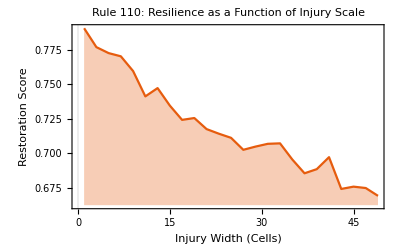

```mathematica
(*Function to calculate the percentage of recovery*)MeasureRecovery[rule_,injuryWidth_]:=Module[{steps=150,mixAt=50,init,clean,injured,diff},init=CenterArray[{1},301];
clean=CellularAutomaton[rule,init,steps];
(*Generate injured state*)injured=Module[{pre,mid,post},pre=Take[clean,mixAt];
mid=Last[pre];
(*Randomly perturb a section of width'injuryWidth'*)mid[[151-injuryWidth;;151+injuryWidth]]=RandomInteger[1,2*injuryWidth+1];
post=CellularAutomaton[rule,mid,steps-mixAt];
Join[pre,post]];
(*Calculate XOR Difference*)diff=MapThread[BitXor,{clean,injured},2];
(*Final row difference:1.0=Perfect recovery,0.0=Total divergence*)1.0-(Total[Last[diff]]/Length[Last[diff]])];

(*Run for Rule 110 across widths 1 to 50*)
data=Table[{w,Mean[Table[MeasureRecovery[110,w],{10}]]},{w,1,50,2}];
ListLinePlot[data,PlotTheme->"Scientific",AxesLabel->{"Injury Width (Cells)","Restoration Score"},PlotLabel->"Rule 110: Resilience as a Function of Injury Scale",Filling->Bottom]
```

```mathematica
(*Sweep all 256 rules for resilience to a 10-cell injury*)allRulesResilience=Table[{r,MeasureRecovery[r,5]},{r,0,255}];

(*Visualize the top 20 most resilient rules*)
topRules=TakeSortBy[allRulesResilience,Last,Greater][[{1;;20}]];
TableForm[topRules,TableHeadings->{None,{"Rule","Resilience Score"}}]
```

Part::pkspec1: The expression {1;;20} cannot be used as a part specification.

TakeSortBy[{{0,1.},{1,0.00996678},{2,0.986711},{3,0.00996678},{4,0.993355},{5,0.0299003},{6,0.976744},{7,0.},{8,1.},{9,0.0332226},{10,0.986711},{11,0.013289},{12,0.986711},{13,0.504983},{14,0.973422},{15,0.0199336},{16,0.986711},{17,0.013289},{18,0.813953},{19,0.00996678},{20,0.980066},{21,0.0299003},{22,0.571429},{23,0.00996678},{24,0.983389},{25,0.0265781},{26,0.747508},{27,0.0299003},{28,0.986711},{29,0.0232558},{30,0.508306},{31,0.0166113},{32,1.},{33,0.0166113},{34,0.983389},{35,0.0365449},{36,0.993355},{37,0.0431894},{38,0.976744},{39,0.00996678},{40,1.},{41,0.0930233},{42,0.983389},{43,0.0299003},{44,0.990033},{45,0.385382},{46,0.973422},{47,0.0332226},{48,0.980066},{49,0.0299003},{50,0.0265781},{51,0.0166113},{52,0.976744},{53,0.013289},{54,0.179402},{55,0.0166113},{56,0.980066},{57,0.166113},{58,0.0265781},{59,0.0332226},{60,0.847176},{61,0.0365449},{62,0.33887},{63,0.0265781},{64,1.},{65,0.0332226},{66,0.983389},{67,0.0431894},{68,0.993355},{69,0.508306},{70,0.976744},{71,0.0166113},{72,0.993355},{73,0.541528},{74,0.973422},{75,0.395349},{76,0.990033},{77,0.983389},{78,0.973422},{79,0.508306},{80,0.983389},{81,0.0299003},{82,0.72093},{83,0.013289},{84,0.973422},{85,0.0299003},{86,0.495017},{87,0.},{88,0.976744},{89,0.388704},{90,0.734219},{91,0.0332226},{92,0.973422},{93,0.511628},{94,0.956811},{95,0.0299003},{96,1.},{97,0.0431894},{98,0.976744},{99,0.169435},{100,0.993355},{101,0.365449},{102,0.847176},{103,0.0199336},{104,1.},{105,0.415282},{106,0.953488},{107,0.0531561},{108,0.990033},{109,0.531561},{110,0.760797},{111,0.0265781},{112,0.973422},{113,0.0365449},{114,0.0199336},{115,0.013289},{116,0.973422},{117,0.0199336},{118,0.332226},{119,0.0299003},{120,0.930233},{121,0.0498339},{122,0.352159},{123,0.0232558},{124,0.76412},{125,0.0398671},{126,0.561462},{127,0.0199336},{128,1.},{129,0.747508},{130,0.983389},{131,0.342193},{132,0.993355},{133,0.963455},{134,0.976744},{135,0.498339},{136,1.},{137,0.760797},{138,0.980066},{139,0.980066},{140,0.983389},{141,0.9701},{142,0.9701},{143,0.973422},{144,0.986711},{145,0.348837},{146,0.787375},{147,0.528239},{148,0.980066},{149,0.475083},{150,0.611296},{151,0.936877},{152,0.983389},{153,0.853821},{154,0.79402},{155,0.986711},{156,0.973422},{157,0.966777},{158,0.259136},{159,0.986711},{160,1.},{161,0.607973},{162,0.980066},{163,0.0332226},{164,0.996678},{165,0.787375},{166,0.9701},{167,0.817276},{168,1.},{169,0.943522},{170,0.973422},{171,0.976744},{172,0.990033},{173,0.980066},{174,0.966777},{175,0.983389},{176,0.980066},{177,0.0265781},{178,0.0166113},{179,0.0199336},{180,0.973422},{181,0.840532},{182,0.79402},{183,0.86711},{184,0.976744},{185,0.976744},{186,0.0199336},{187,0.986711},{188,0.734219},{189,0.986711},{190,0.501661},{191,0.993355},{192,1.},{193,0.76412},{194,0.983389},{195,0.847176},{196,0.983389},{197,0.990033},{198,0.986711},{199,0.986711},{200,0.986711},{201,0.986711},{202,0.644518},{203,0.986711},{204,0.980066},{205,0.990033},{206,0.9701},{207,0.986711},{208,0.983389},{209,0.980066},{210,0.770764},{211,0.983389},{212,0.973422},{213,0.980066},{214,0.272425},{215,0.993355},{216,0.644518},{217,0.996678},{218,0.202658},{219,0.996678},{220,0.976744},{221,0.993355},{222,0.986711},{223,1.},{224,1.},{225,0.913621},{226,0.9701},{227,0.973422},{228,0.993355},{229,0.963455},{230,0.744186},{231,0.983389},{232,0.963455},{233,0.993355},{234,0.634551},{235,1.},{236,0.993355},{237,0.993355},{238,0.980066},{239,1.},{240,0.973422},{241,0.973422},{242,0.00664452},{243,0.983389},{244,0.966777},{245,0.980066},{246,0.508306},{247,0.990033},{248,0.637874},{249,1.},{250,0.342193},{251,1.},{252,0.983389},{253,1.},{254,0.993355},{255,1.}},Last,Greater]⟦{1;;20}⟧

```mathematica
(*1. Setup Parameters*)rule=30; (*The rule we are studying*)
steps1=50; (*Initial evolution time*)
steps2=100; (*Time after mixing*)
perturbWidth=20; (*How many cells to'mix up'*)
(*2. Run the initial evolution*)
init=CenterArray[{1},201];
evolution1=CellularAutomaton[rule,init,steps1];
latestState=Last[evolution1];
(*3. Mix up the latest cells*)
(*We replace a central block with random 0s and 1s*)
mid=IntegerPart[Length[latestState]/2];
perturbedState=latestState;
perturbedState⟦mid-perturbWidth;;mid+perturbWidth⟧=RandomInteger[1,2*perturbWidth+1];
(*4. Run the recovery evolution*)
evolution2=CellularAutomaton[rule,perturbedState,steps2];
(*5. Visualize the result*)
ArrayPlot[Join[evolution1,evolution2],Mesh->True,ColorRules->{0->White,1->Black},Epilog->{Red,Thickness[0.005],Line[{{0,steps2+steps1-steps1},{201,steps2+steps1-steps1}}]},PlotLabel->"Pattern Restoration Experiment (Red Line = Mixing Point)"]
```

-Graphics-

```mathematica
-Graphics-(*1. Setup Parameters*)rule=30;
steps1=50;
steps2=100;
perturbWidth=20;

(*2. Initial evolution (Common to both)*)
init=CenterArray[{1},201];
evolution1=CellularAutomaton[rule,init,steps1];
latestState=Last[evolution1];

(*3. Branching:Control vs Perturbed*)
(*Control:No changes*)
controlEvolution2=CellularAutomaton[rule,latestState,steps2];

(*Perturbed:Mix up the central cells*)
mid=IntegerPart[Length[latestState]/2];
perturbedState=latestState;
perturbedState[[mid-perturbWidth;;mid+perturbWidth]]=RandomInteger[1,2*perturbWidth+1];
experimentEvolution2=CellularAutomaton[rule,perturbedState,steps2];

(*4. Visualization*)
controlPlot=ArrayPlot[Join[evolution1,controlEvolution2],ColorRules->{0->White,1->Black},PlotLabel->"Control (No Injury)"];

experimentPlot=ArrayPlot[Join[evolution1,experimentEvolution2],ColorRules->{0->White,1->Black},Epilog->{Red,Thickness[0.01],Line[{{0,steps2+steps1-steps1},{201,steps2+steps1-steps1}}]},PlotLabel->"Experiment (With Injury)"];

GraphicsGrid[{{controlPlot,experimentPlot}},ImageSize->Large]
```

Set::write: Tag Times in … is Protected.

-Graphics-

```mathematica
(*1. Setup Parameters*)rule=30; (*The rule under study[cite:1,5,207]*)
steps1=50; (*Initial evolution time[cite:3,6,210]*)
steps2=100; (*Time after mixing[cite:4,6,211]*)
perturbWidth=20; (*Width of the'mixed' region[cite:6,212]*)
(*2. Initial Evolution*)
init=CenterArray[{1},201];[cite:8,214]
evolution1=CellularAutomaton[rule,init,steps1];[cite:9,215]
latestState=Last[evolution1];[cite:10,216]
(*3. Mixing/Perturbation*)
mid=IntegerPart[Length[latestState]/2];[cite:13,218]
perturbedState=latestState;[cite:14,219]
(*Corrected syntax for part assignment[cite:220]*)
perturbedState⟦mid-perturbWidth;;mid+perturbWidth⟧=RandomInteger[1,2*perturbWidth+1];[cite:15,221]
(*4. Recovery Evolution*)
evolution2=CellularAutomaton[rule,perturbedState,steps2];[cite:17,223]
(*5. Visualization*)
ArrayPlot[Join[evolution1,evolution2],Mesh->True,ColorRules->{0->White,1->Black},[cite:19,20,225,226] Epilog->{Red,Thickness[0.005],Line[{{0,steps1},{201,steps1}}]},(*Fixed coordinate to the mixing point[cite:226]*)PlotLabel->"Pattern Restoration Experiment (Red Line = Mixing Point)"][cite:21,227]
```

Null[cite:8,214]

Null[cite:9,215]

Null[cite:10,216]

Null[cite:13,218]

Null[cite:14,219]

Null[cite:15,221]

Null[cite:17,223]

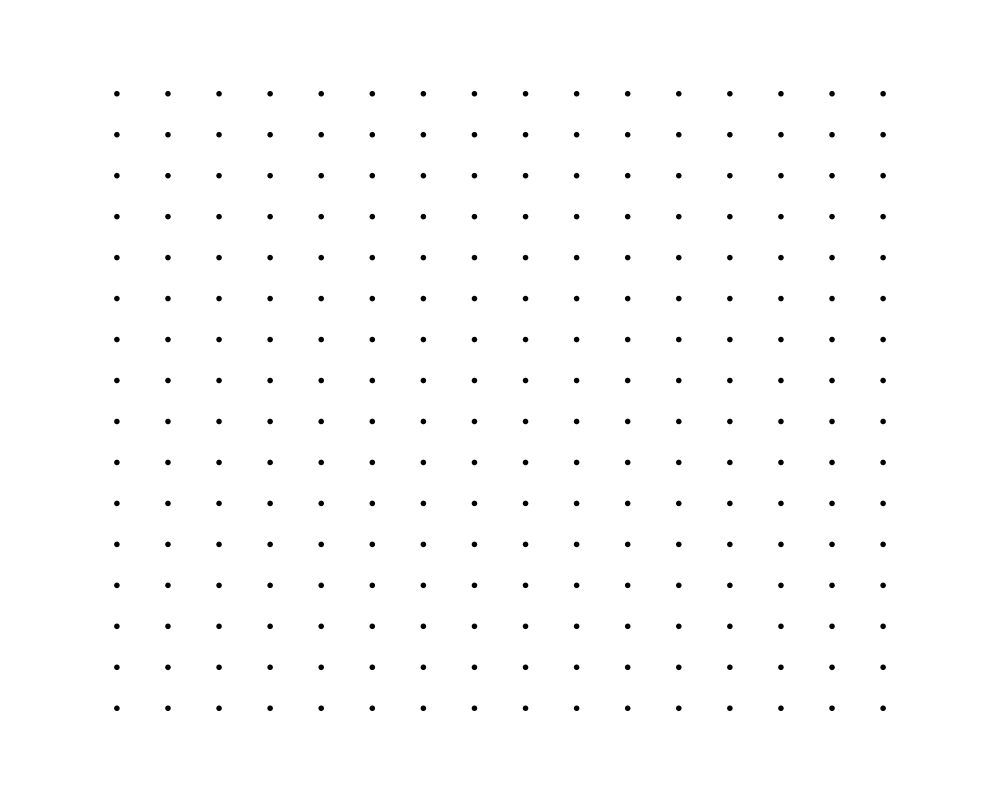

```mathematica
(*Ruliological Sweep of All 256 Rules*)stepsBefore=100;
stepsAfter=50;
width=201;
results=Table[Module[{init,clean,mixed,diff,midRow,perturbWidth=10},init=CenterArray[{1},width];
(*1. The'Clean' Path*)clean=CellularAutomaton[rule,init,stepsBefore+stepsAfter];
(*2. The'Mixed' Path (Interrupt at Row 100)*)midState=clean⟦stepsBefore+1⟧;
(*Randomize a section of the row*)perturbedState=ReplacePart[midState,Thread[Range[101-perturbWidth,101+perturbWidth]->RandomInteger[1,2 perturbWidth+1]]];
mixed=Join[Take[clean,stepsBefore],CellularAutomaton[rule,perturbedState,stepsAfter]];
(*3. The Difference Map (XOR)*)diff=MapThread[BitXor,{clean,mixed},2];
(*Return a small plot for each rule*)ArrayPlot[diff,ColorRules->{1->Red,0->White},Frame->False,PlotLabel->Style[rule,8]]],{rule,0,255}];
(*Display as a 16x16 grid*)
GraphicsGrid[Partition[results,16],ImageSize->1000]
```

```mathematica
(*1. Setup Parameters*)rule=30; (*The rule under study[cite:1,5,207]*)
steps1=50; (*Initial evolution time[cite:3,6,210]*)
steps2=100; (*Time after mixing[cite:4,6,211]*)
perturbWidth=20; (*Width of the'mixed' region[cite:6,212]*)
(*2. Initial Evolution*)
init=CenterArray[{1},201];[cite:8,214]
evolution1=CellularAutomaton[rule,init,steps1];[cite:9,215]
latestState=Last[evolution1];[cite:10,216]
(*3. Mixing/Perturbation*)
mid=IntegerPart[Length[latestState]/2];[cite:13,218]
perturbedState=latestState;[cite:14,219]
(*Corrected syntax for part assignment[cite:220]*)
perturbedState⟦mid-perturbWidth;;mid+perturbWidth⟧=RandomInteger[1,2*perturbWidth+1];[cite:15,221]
(*4. Recovery Evolution*)
evolution2=CellularAutomaton[rule,perturbedState,steps2];[cite:17,223]
(*5. Visualization*)
ArrayPlot[Join[evolution1,evolution2],Mesh->True,ColorRules->{0->White,1->Black},[cite:19,20,225,226] Epilog->{Red,Thickness[0.005],Line[{{0,steps1},{201,steps1}}]},(*Fixed coordinate to the mixing point[cite:226]*)PlotLabel->"Pattern Restoration Experiment (Red Line = Mixing Point)"][cite:21,227]
```

Null[cite:8,214]

Null[cite:9,215]

Null[cite:10,216]

Null[cite:13,218]

Null[cite:14,219]

Null[cite:15,221]

Null[cite:17,223]

```mathematica
(*Define Parameters*)ruleNumber=110;steps=200;gridSize=200;noiseProb=0.02;

(*Initial State:Single Seed*)initialState=CenterArray[1,gridSize];

(*Function to evolve with noise*)evolveWithNoise[state_,rule_]:=Module[{nextState,noiseMask},nextState=CellularAutomaton[rule,state,1][[2]];noiseMask=RandomChoice[{1-noiseProb,noiseProb}->{0,1},gridSize];BitXor[nextState,noiseMask]];

(*Run the simulation*)stochasticEvolution=NestList[evolveWithNoise[#,ruleNumber]&,initialState,steps];

(*Visualize Results*)ArrayPlot[stochasticEvolution,ColorRules->{0->White,1->Black},Mesh->False,Frame->True,FrameLabel->{"Cell Index","Time Step"},PlotLabel->"Rule "<>ToString[ruleNumber]<>" with "<>ToString[noiseProb*100]<>"% Continuous Noise"]
```

-Graphics-

```mathematica
(*Parameters*)rule=110;steps=200;gridSizes={50,100,200,500};injuryWidth=10;injuryTime=50;

(*Function to calculate restoration for a specific size) testSize[L_]:=Module[{control,injury,diff},(Control Evolution*)control=CellularAutomaton[rule,CenterArray[1,L],steps];

(*Create Injury at injuryTime*)injuredState=control[[injuryTime+1]];mid=Floor[L/2];injuredState[[mid-Floor[injuryWidth/2];;mid+Floor[injuryWidth/2]]]=RandomInteger[{0,1},injuryWidth+1];

(*Evolve Injury*)injury=CellularAutomaton[rule,injuredState,steps-injuryTime];

(*Compare only the steps after injury*)diff=Total[BitXor[control[[injuryTime+1;;]],injury],2];

(*Return 1 if healed (diff is 0),0 otherwise*)If[diff==0,1,0]];

(*Run the loop and print results*)results=Table[{s,testSize[s]},{s,gridSizes}];Print["Grid Size vs Healing Success (1=Healed, 0=Failed): ",results]
```

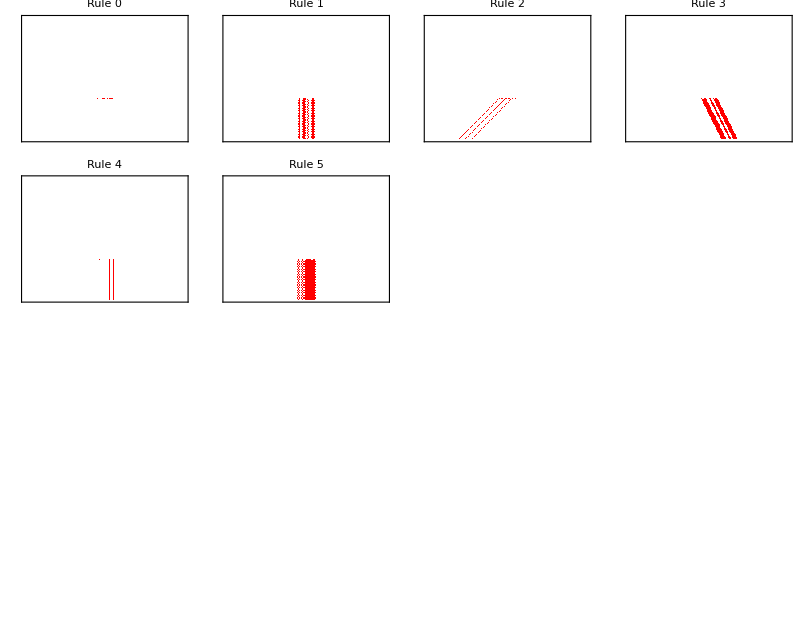

```mathematica
(*Parameters*)stepsBefore=100;
stepsAfter=50;
width=201;
perturbWidth=10;

(*Function to generate a single rule plot*)
generateRulePlot[rule_]:=Module[{init,clean,midState,perturbedState,mixed,diff},init=CenterArray[{1},width];
clean=CellularAutomaton[rule,init,stepsBefore+stepsAfter];
midState=clean[[stepsBefore+1]];
perturbedState=ReplacePart[midState,Thread[Range[101-perturbWidth,101+perturbWidth]->RandomInteger[1,2 perturbWidth+1]]];
mixed=Join[Take[clean,stepsBefore],CellularAutomaton[rule,perturbedState,stepsAfter]];
diff=MapThread[BitXor,{clean,mixed},2];
ArrayPlot[diff,ColorRules->{1->Red,0->White},Frame->True,FrameTicks->None,PlotLabel->Style["Rule "<>ToString[rule],10]]];

(*Generate all 256 plots*)
allPlots=Table[generateRulePlot[r],{r,0,255}];

(*Partition into 16 groups (16 rules each)*)
figureGroups=Partition[allPlots,16];

(*Display the first group (Rules 0-15) as an example*)
(*To export all 16,you would loop this or use Export[]*)
GraphicsGrid[Partition[figureGroups[[1]],4],ImageSize->800,Spacings->10]
```

```mathematica
(*1. Setup Directories*)exportFolder=FileNameJoin[{$HomeDirectory,"Desktop","Individual_Rule_Panels"}];
If[!FileExistsQ[exportFolder],CreateDirectory[exportFolder]];

(*2. Parameters*)
stepsBefore=100;
stepsAfter=50;
width=201;
perturbWidth=10;

(*3. Generation and Export Loop*)
Do[Module[{init,clean,midState,perturbedState,mixed,diff,plot,fileName},(*Generate original CA evolution*)init=CenterArray[{1},width];
clean=CellularAutomaton[rule,init,stepsBefore+stepsAfter];
(*Capture state at the perturbation point*)midState=clean[[stepsBefore+1]];
(*Create perturbed state by flipping bits in the center*)perturbedState=ReplacePart[midState,Thread[Range[101-perturbWidth,101+perturbWidth]->RandomInteger[1,2 perturbWidth+1]]];
(*Generate evolution from the perturbed state*)mixed=Join[Take[clean,stepsBefore],CellularAutomaton[rule,perturbedState,stepsAfter]];
(*Calculate the Difference Map (XOR) to isolate the error cone*)diff=MapThread[BitXor,{clean,mixed},2];
(*Create the individual plot for this rule*)plot=ArrayPlot[diff,ColorRules->{1->Red,0->White},Frame->True,FrameTicks->None,ImageSize->400,PlotLabel->Style["Rule "<>ToString[rule],14,Bold]];
(*Export as a singular PNG for this specific rule*)(*IntegerString with 10,3 ensures files are named Rule_000.png,Rule_001.png,etc.*)fileName=FileNameJoin[{exportFolder,"Rule_"<>IntegerString[rule,10,3]<>".png"}];
Export[fileName,plot,"PNG"];
(*Progress tracking*)If[Mod[rule,32]==0,Print["Processing Rule: ",rule]];],{rule,0,255}];

Print["Done! 256 individual panels have been saved to the 'Individual_Rule_Panels' folder on your Desktop."];
```

Processing Rule: 0

Processing Rule: 32

Processing Rule: 64

Processing Rule: 96

Processing Rule: 128

Processing Rule: 160

Processing Rule: 192

Processing Rule: 224

Done! 256 individual panels have been saved to the 'Individual_Rule_Panels' folder on your Desktop.

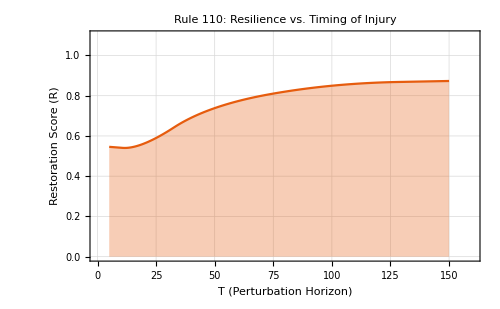

```mathematica
(*Parameters*)rule=110;
gridSize=301;
steps=300;
injuryWidth=10;
tHorizons={5,20,50,100,150}; (*Testing different T values*)

(*Reuse the CalculateResilience logic but make T a variable*)
testTIndependence[rule_,t_]:=Module[{init,clean,injured,diff,score},init=CenterArray[1,gridSize];
clean=CellularAutomaton[rule,init,steps];
(*Apply disruption at time T*)mid=clean[[t+1]];
mid[[Floor[gridSize/2]-injuryWidth;;Floor[gridSize/2]+injuryWidth]]=RandomInteger[1,2*injuryWidth+1];
(*Evolve injured state for the remaining steps*)post=CellularAutomaton[rule,mid,steps-t];
injured=Join[Take[clean,t],post];
(*Difference Map and Score*)diff=MapThread[BitXor,{clean,injured},2];
score=1.0-(Total[Last[diff]]/gridSize);
score];

(*Run Sampling*)
tData=Table[{t,Mean[Table[testTIndependence[rule,t],{10}]]},{t,tHorizons}];

(*Visualize results*)
ListLinePlot[tData,PlotTheme->"Scientific",Frame->True,FrameLabel->{"T (Perturbation Horizon)","Restoration Score (R)"},PlotLabel->Style["Rule "<>ToString[rule]<>": Resilience vs. Timing of Injury",14,Bold],PlotRange->{{0,160},{0,1.1}},Filling->Bottom,ImageSize->500,ImagePadding->{{60,20},{50,20}},(*Adjusts space for the labels*)GridLines->Automatic,InterpolationOrder->2]
```